```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA",
ExcludeParticles->{S[1],V[1],V[2],V[3],V[4],U[1],U[2],U[3],U[4],U[5],F[14]},InsertionLevel-> {Particles},GenericModel->"../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA_FC"
];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
tops = CreateTopologies[1,1->3,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { F[14]} -> {F[12],-F[12], F[13]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},
ExcludeParticles->{V[1],V[2],V[3],V[4],U[1],U[2],U[3],U[4],U[5],F[14],S[3],S[2],S[4]},
ExcludeFieldPoints-> {FieldPoint[_][F[14],S[4],-F[13]],FieldPoint[_][F[14],S[1],-F[13]],FieldPoint[_][S[4],S[1],S[1]],FieldPoint[_][S[4],S[4],S[1]],FieldPoint[_][S[1],S[1],S[1]],FieldPoint[_][S[4],S[4],S[4]],FieldPoint[_][F[14],S[1],S[1],-F[13]]}];
```

generic model {../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA_FC} initialized

classes model {../models/DipoleDM2/DipoleDM2_minimalH_FA/DipoleDM2_minimalH_FA} initialized

in total: 2 Particles insertions

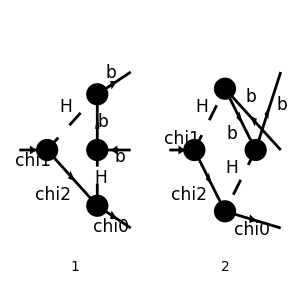

```mathematica
(* goodDiags=DiagramExtract[allDiags,{2,3}];*)
goodDiags=allDiags;
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True,GaugeRules->{GaugeXi[S[_]]->1}]/.{SUNT->FASUNT},IncomingMomenta->{k},LorentzIndexNames->{μ,ν},OutgoingMomenta->{-p1,-p2,-p},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[FCReplaceMomenta[SUNSimplify[DiracSimplify[ampA]],{p4-> -p1-p2-p}]]]
```

in total: 2 Particles amplitudes

1/4 sina^2 (sina^2-1) yb^2 ychi1x3 ychi2x3 δ_bc2 (((M2-MB) γ·p2+γ·q (M2-MB-2 γ·p2)+M2 MB-γ·p (MB+γ·p2+γ·q)-γ·p1 (MB+γ·p2+γ·q)-p2^2-q^2)/((q^2-MH^2).((p2+q)^2-MB^2).((p1+p2+q)^2-MH^2).((p+p1+p2+q)^2-M2^2))+(-γ·p1 (M2+MB-γ·p2-2 γ·q)-γ·q (M2+MB-γ·p2)+M2 MB+γ·p (-MB+γ·p1+γ·q)-MB γ·p2+p1^2+q^2)/((q^2-MH^2).((p1+q)^2-MB^2).((p1+p2+q)^2-MH^2).((p+p1+p2+q)^2-M2^2)))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k,p1,p2,p,M1,MB,MB,M0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u->  M1^2+M0^2};
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(C_0(M0^2,MB^2,s,M2^2,MH^2,MB^2) | 0
C_0(M0^2,MB^2,t,M2^2,MH^2,MB^2) | 0
D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2) | 0
D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2) | 0
D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2) | 0
D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2) | 0
D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2) | 0
D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2) | 0
D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2) | 0
D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2) | 0)

```mathematica
ampSquared=1/2 (ampEsimp2 (ComplexConjugate[ampEsimp2]))//Simplify;
```

```mathematica
ampSquared
```

1/32 π^4 sina^4 (1-sina^2) (sina^2-1) yb^4 ychi1x3^2 ychi2x3^2 (D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2) M0^2-D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2) M0^2+C_0(M0^2,MB^2,s,M2^2,MH^2,MB^2)-C_0(M0^2,MB^2,t,M2^2,MH^2,MB^2)-2 MB^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)+MH^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)+M2 MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)+2 MB^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)-MH^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+M2 MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)-MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2) γ·p-MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2) γ·p-M2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2) γ·p1+D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2) γ·p γ·p1+M2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2) γ·p2-D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2) γ·p γ·p2-2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2) γ·p1 γ·p2+2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2) γ·p1 γ·p2-M2 γ·p D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)-MB γ·p D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)+2 γ·p γ·p1 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)+γ·p γ·p2 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)+M2 γ·p D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)-MB γ·p D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)-γ·p γ·p1 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)-2 γ·p γ·p2 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)-MB^2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)+M2 γ·p2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)+MB γ·p2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)-γ·p γ·p2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)-2 γ·p1 γ·p2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)+MB^2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)-M2 γ·p1 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)+MB γ·p1 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)+γ·p γ·p1 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)+2 γ·p1 γ·p2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)-3 MB^2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+M2 γ·p1 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+MB γ·p1 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-γ·p γ·p1 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+M2 γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+MB γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-γ·p γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-3 γ·p1 γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+3 MB^2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)-M2 γ·p1 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)+MB γ·p1 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)+γ·p γ·p1 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)-M2 γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)+MB γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)+γ·p γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)+3 γ·p1 γ·p2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)) (-D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2) M0^2+D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2) M0^2-C_0(M0^2,MB^2,s,M2^2,MH^2,MB^2)+C_0(M0^2,MB^2,t,M2^2,MH^2,MB^2)+2 MB^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)-MH^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)-M2 MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)-2 MB^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+MH^2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)-M2 MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+γ·p (MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)+MB D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+M2 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)+MB D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)-M2 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)+MB D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2))+MB^2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)-MB^2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)+3 MB^2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+FeynCalc`ComplexConjugate`Private`diracChainCC(γ·p1 γ·p2) (2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)-2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)-2 D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)+3 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-3 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2))+FeynCalc`ComplexConjugate`Private`diracChainCC(γ·p γ·p2) (D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)-D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)+2 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)+D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)+D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2))-3 MB^2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)-FeynCalc`ComplexConjugate`Private`diracChainCC(γ·p γ·p1) (D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+2 D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,s,MH^2,M2^2,MH^2,MB^2)-D_1(M0^2,M1^2-2 MB^2,MB^2,MB^2,u,t,MH^2,M2^2,MH^2,MB^2)+D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)-D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2))+γ·p1 (M2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,t,u,M2^2,MH^2,MB^2,MH^2)+(M2-MB) D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,t,MH^2,MB^2,MH^2,M2^2)-M2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-MB D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+M2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)-MB D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2))-γ·p2 (M2 D_0(M0^2,MB^2,MB^2,M1^2-2 MB^2,s,u,M2^2,MH^2,MB^2,MH^2)+(M2+MB) D_1(MB^2,MB^2,M0^2,M1^2-2 MB^2,u,s,MH^2,MB^2,MH^2,M2^2)+M2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)+MB D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,s,u,MB^2,MH^2,M2^2,MH^2)-M2 D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2)+MB D_1(MB^2,M1^2-2 MB^2,M0^2,MB^2,t,u,MB^2,MH^2,M2^2,MH^2))) δ_bc2^2